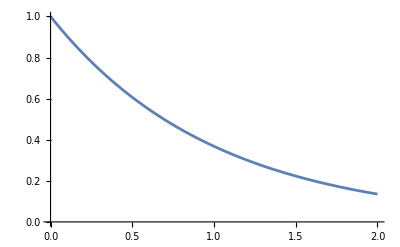

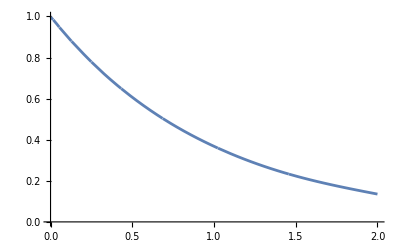

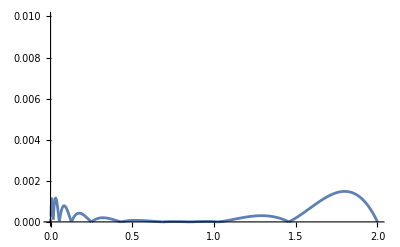

125/4 (7/250+3 (1/7 (1/ⅇ^(2/125)-1/ⅇ^(1/500))+7 (-1+1/ⅇ^(1/500))))

```mathematica
(* Дефинираме функцията и броя на възлите *)
f[t_]:=Exp[-t];
df[t_]:=-Exp[-t];

interval={0,2};
n=10;

(* Създаваме възлите *)
Do[x[k] = 2*(k/n)^3, {k, 0, n+1}];

(* Смятаме разстоянието между 2 поредни възела и разделената разлика *)
Do[delta[k]=x[k+1]-x[k],{k,0,n}];
Do[razdRazl[k]=(f[x[k]]-f[x[k-1]]) / delta[k - 1],{k,1,n + 1}];

(* Дефинираме b[i], за да съставим системата *)
Do[b[i] = 3(delta[i] * razdRazl[i] + delta[i -1] * razdRazl[i + 1]), {i, 1, n}];

(* Гранични условия *)
d[0] = df[x[0]];
d[n+1] = df[x[n + 1]];

(* Добавяме граничните условия в системата *)
b'[1]=b[1] -delta[1]d[0];
b'[n]=b[n]-delta[n-1]d[n+1];
Do[b'[i]=b[i], {i, 2, n-1}] ;

(* Решаваме с метод на прогонката получената система *)
(* Алфа и Бета от http://fmi.wikidot.com/chm9 *)
A[1] = -delta[0]/(2(delta[0] + delta[1]));
B[1] = b'[1]/(2(delta[0] + delta[1]));

Do[
{
A[i] = -delta[i-1 ]/(2(delta[i-1] + delta[i]) + delta[i]A[i-1]),
B[i] = (b'[i] - delta[i]B[i-1])/(2(delta[i-1] + delta[i]) + delta[i]A[i-1])
},
{i, 2, n}
];

(* Връщаме се назад *)
d[n] = beta[n];
Do[d[i]=alpha[i]d[i+1]+beta[i],{i,n-1,1,-1}];

(* Преизчисляваме коефициентите използвани за интерполцията на Нютон *)
Do[
{
constant[i]=f[x[i]],
lin[i]=d[i],
kvad[i]=(razdRazl[i+1]-d[i])/delta[i],
kub[i]=(d[i+1]-2razdRazl[i+1]+d[i])/(delta[i]delta[i])
},
{i, 0, n}
];

(* Използваме формула на Нютон за интерполация *)
s[t_] := Sum[
If[x[i]<=t<=x[i+1],
constant[i] + lin[i]*(t-x[i])+
kvad[i] * (t-x[i]) * (t-x[i])+
kub[i] * (t-x[i])(t-x[i])*(t-x[i+1]),
0
],
{i, 0, n-1}
];


Plot[f[t],{t,0,2},PlotRange->{interval,{0,1}}]
Plot[s[t],{t,0,2},PlotRange->{interval,{0,1}}]
Plot[Abs[f[t]-s[t]],{t,0,2},PlotRange->{interval,{0,0.01}}]
```